```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)

(*ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/20230919/Ren2015_H0d1_T1d2_potential/result.json"
*)
ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d1_T1d2.csv"];
name="/Volumes/home/BEM/20230919/Ren2015_H0d1_T1d2_potential_2/result.json"
FindFile[name]
```

/Volumes/home/BEM/20230919/Ren2015_H0d1_T1d2_potential_2/result.json

/Volumes/home/BEM/20230919/Ren2015_H0d1_T1d2_potential_2/result.json

```mathematica
imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
```

```mathematica
titles=imported[[;;,1]];
Column[titles,Background->{{LightGreen,Green}},Frame->True]
```

cpu_time
float_COM
float_EK
float_EP
float_accel
float_area
float_force
float_pitch
float_roll
float_torque
float_velocity
float_yaw
simulation_time
wall_clock_time
water_E
water_EK
water_EP
water_volume

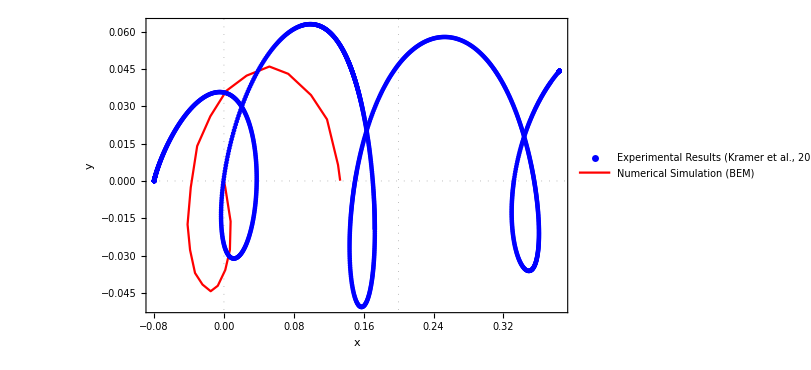

```mathematica
ListPlot[
{{getData["float_COM",1]-2.08,getData["float_COM",3]-0.4}ᵀ
,{#1,#2}&@@@ExperimentData},
PlotRange->All,
Joined->{False,True},
PlotStyle->{{Blue,Dashed},{Red}},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
(*AspectRatio->1/2,*)
(*GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},*)
Frame->True,
FrameLabel->{
Style["x",FontSize->20,FontFamily->"Times",Italic],
Style["y",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

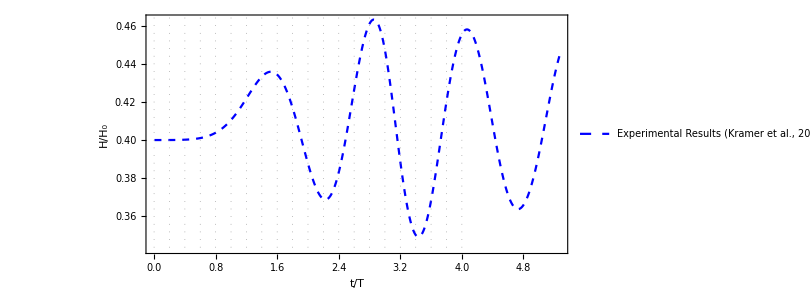

```mathematica
fig=ListPlot[
{getData["simulation_time"],getData["float_COM",3]}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

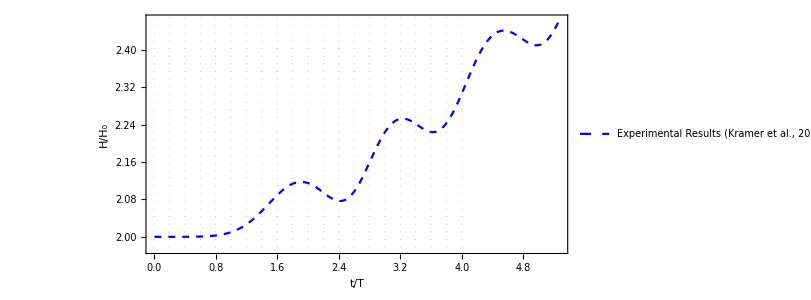

```mathematica
ListPlot[
{getData["simulation_time"],getData["float_COM",1]}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

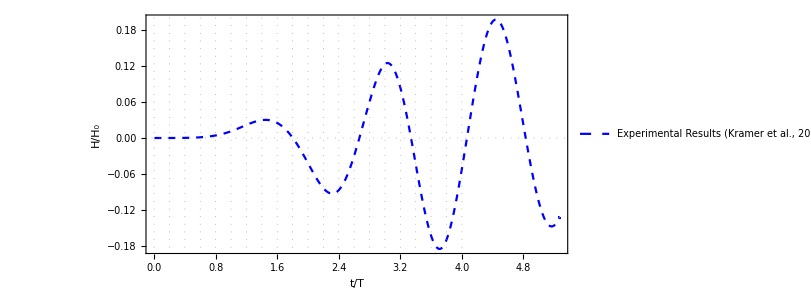

```mathematica
ListPlot[
{getData["simulation_time"],getData["float_pitch"]}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

```mathematica
Total[Table[i,{i,1,100}]]
```

5050

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}